```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Define synchronization condition for driving strength*)
f[A_,m_,M_,n_]:= A / Sqrt[((4*m*M)/n)^2-1]
```

```mathematica
??f
```

```mathematica
n=7;
M=2;
A= 431; (*parallel hyperfine component in units of kHz, examples are: strongly coupled A=431 kHz, weakly coupled A=89kHz*)
```

```mathematica
Om = N[Table[f[A,m,M,n],{m,1,10,1}]] 
(*driving strength Omega in units of kHz, a function of M*)
(*Falls m ungerade, muss M/2 el positiveInteger sein, ansonsten muss eine Einzelqubitgatter Phasenkorrektur durchgeführt werden*)
(*value from Taminau group is approx 1 KHz*)
```

{209.696,96.6213,63.5334,47.4251,37.8577,31.511,26.9903,23.6056,20.9762,18.8743}

```mathematica
(*calculate gate time tg as a function of omega. Values from Taminau group are approx 700-800 microseconds*)
tg[O_]:=n*1000/(2*O)
```

```mathematica
tglist=tg[Om]
```

{16.6908,36.2239,55.0891,73.8005,92.4515,111.072,129.676,148.27,166.856,185.437}

```mathematica
values1 = Thread[{Om,tglist}]
```

{{54.3009,9.20795},{26.9903,18.5252},{17.9739,27.818},{13.4753,37.1048},{10.7784,46.3892},{8.98112,55.6724},{7.69766,64.9548},{6.7352,74.2369},{5.98669,83.5186},{5.38792,92.8002}}

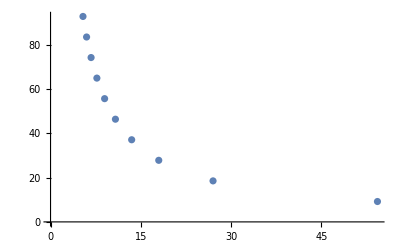

```mathematica
ListPlot[values1] (*total gate time in units of microseconds*)
```

```mathematica
(*ich meine klar, wenn ich alles festhalte und mit M hochgehe, wird die Gatterzeit länger, aber das ist ja keine so große Erkenntnis. Ich glaube, die Taminiau-Gruppe hat das so gemacht, weil sie mit einem sehr geringem Feld getrieben haben. Eigentlich machte es bei dem Schema hier keinen Sinn, weil ja alle anderen Spins als Rauschen bewertet werden und nicht kohärent kontrolliert werden müssen. Ich glaube die relevantere Frage ist, wie stark das externe B-Feld ist.*)


(*tg=28 or 58 microseconds are first minimal gate times for strongly coupled 13C spin (A=431kHz) for all values of n. Corresponding values are Bext`l*64 Gauss and omega=54kHz re omega=26 kHz for M=2 re M=4, m=n=1.) HIgher values for m lead to lower omega and higher values for n lead to a higher omega. Higher values for m lead to higher gate time and lower driving strength. Higher values for n lead to a stronger driving field but only to a minimally lower gate time.
For weakly coupled spins (i.e.A=90kHz) we have Omega=11.2 or Omega=5.6 kHz and tg=140 or tg=278 for M=4*)
```